## Definitions and Functions

Dimensionla analysis:

```mathematica
Solve[{a u^βxu x^βxx y^βxy-b u^αxu x^αxx y^αxy==0,c u^βyu x^βyx y^βyy-d u^αyu x^αyx y^αyy==0},{x,y}]//.ⅇ^((x_+y_)/z_):>ⅇ^(x/z)ⅇ^(y/z)//.ⅇ^x_Log[a_]:>a^x//FullSimplify
```

{{x→a^((-αyy+βyy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) b^((-αyy+βyy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((-αxy+βxy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxy+βxy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) u^((-(αxy-βxy) (αyu-βyu)+(αxu-βxu) (αyy-βyy))/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))),y→a^((-αyx+βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) b^((αyx-βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((αxx-βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxx+βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) u^((-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx))/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy)))}}

```mathematica
{a u^βxu x^βxx y^βxy-b u^αxu x^αxx y^αxy,c u^βyu x^βyx y^βyy-d u^αyu x^αyx y^αyy}/.{x->x/(a^((-αyy+βyy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) b^((-αyy+βyy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((-αxy+βxy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxy+βxy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) u^((-(αxy-βxy) (αyu-βyu)+(αxu-βxu) (αyy-βyy))/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy)))),y->y/(a^((-αyx+βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) b^((αyx-βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((αxx-βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxx+βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) u^((-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx))/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))))}//PowerExpand
```

```mathematica
{dx/dt==a u^βxu x^βxx y^βxy-b u^αxu x^αxx y^αxy,
dy/dt==c u^βyu x^βyx y^βyy-d u^αyu x^αyx y^αyy}
```

```mathematica
{dx/dt==a yst^βxy u^βxu x^βxx y^βxy-b yst^αxy u^αxu x^αxx y^αxy,
dy/dt==c yst^(βyy-1) u^βyu x^βyx y^βyy-d yst^(αyy-1)u^αyu x^αyx y^αyy}
```

```mathematica
Solve[{0==a yst^βxy u^βxu x^βxx y^βxy-b yst^αxy u^αxu x^αxx y^αxy,
0==c yst^(βyy-1) u^βyu x^βyx y^βyy-d yst^(αyy-1)u^αyu x^αyx y^αyy},{x,y}]/.yst->a^((-αyx+βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) b^((αyx-βyx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((αxx-βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxx+βxx)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) u^((-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx))/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy)))//.ⅇ^((x_+y_)/z_):>ⅇ^(x/z)ⅇ^(y/z)//.ⅇ^x_Log[a_]:>a^x//FullSimplify
```

{{x→a^((-αyy+βyy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) b^((-αyy+βyy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) c^((-αxy+βxy)/(-(αxy-βxy) (αyx-βyx)+(αxx-βxx) (αyy-βyy))) d^((-αxy+βxy)/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))) u^((-(αxy-βxy) (αyu-βyu)+(αxu-βxu) (αyy-βyy))/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))),y→1}}

```mathematica
var[x_]:=Union@DeleteCases[Flatten[{Expand[x]//.Plus|Power|Times->List}],_Integer]
eq={ u^βxu x^βxx y^βxy- u^αxu x^αxx y^αxy,T(u^βyu x^βyx y^βyy- u^αyu x^αyx y^αyy)};
param =  {βxu,βxx,βxy,βyu,βyx,βyy,αxu,αxx,αxy,αyu,αyx,αyy};
EQP[z_,T_]:= {u^βxu x^βxx y^βxy- u^αxu x^αxx y^αxy,T(u^βyu x^βyx y^βyy- u^αyu x^αyx y^αyy)}/.Thread[param-> z]
J=Eigenvalues@D[eq,{{x,y}}]//FullSimplify;
```

```mathematica
{Det@#,Tr@#}&@D[eq,{{x,y}}]//FullSimplify
```

{1/(x y)(T u^αyu x^αyx y^αyy (u^αxu x^αxx y^αxy (-αxy αyx+αxx αyy)+u^βxu x^βxx y^βxy (-αyy βxx+αyx βxy))+T u^βyu x^βyx y^βyy (u^αxu x^αxx y^αxy (αxy βyx-αxx βyy)+u^βxu x^βxx y^βxy (-βxy βyx+βxx βyy))),-u^αxu x^(-1+αxx) y^αxy αxx-T u^αyu x^αyx y^(-1+αyy) αyy+u^βxu x^(-1+βxx) y^βxy βxx+T u^βyu x^βyx y^(-1+βyy) βyy}

```mathematica
exchangeRule = Thread[{βyu,βyy,βyz,βzu,βzy,βzz,αyu,αyy,αyz,αzu,αzy,αzz}->param];
```

```mathematica
DPlot[z_,T_,U_,u0_]:=Plot[Evaluate[{x[t],y[t]}/.#],{t,0,30},PlotRange->All,PlotLabel->{Style[TableForm@Thread[{x', y'}==EQP[z,T]],20],FullSimplify@PowerExpand@(Eigenvalues@(D[EQP[z,T],{{x,y}}])/.({x->u^(((-αxy+βxy) (αyu-βyu)+(αxu-βxu) (αyy-βyy))/((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy))),y->1}/.Thread[param->z]))}]&@NDSolve[Join[Thread[{x'[t],y'[t]}==Evaluate[EQP[z,T]/.{u->U,x->x[t],y->y[t]}]],({x[0]==u0,y[0]==1}/.Thread[param->z])],{x[t],y[t]},{t,0,30}]
```

Counting circuits in each category:

## All Circuits

```mathematica
Length[all=Flatten[Outer[List,##]&@@Array[{-1,0,1}&,12],11]]
```

531441

## Connected Circuits

```mathematica
s=Solve[Thread[eq==0],{x,y}][[1]]//FullSimplify;
Length[all=Flatten[Outer[List,##]&@@Array[{-1,0,1}&,12],11]];
Length[Connected = Select[all,(((αxu≠ 0 ||αyu≠ 0 ||βxu≠ 0 ||βyu≠ 0 )  && (αxu≠ 0 ||αxy≠ 0 ||βxu≠ 0 ||βxy≠ 0 ||αyx ≠0 || βyx ≠0) &&(αyu≠ 0 ||αyx≠ 0 ||βyu≠ 0 ||βyx≠ 0 ||αxy ≠0 || βxy ≠0))/.Thread[param->#])&]];
```

## Steady State Exists Circuits

```mathematica
Length[SteadyStateExists = Select[Connected,((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy)/.Thread[param->#])≠ 0&]];
```

There exist T || u such that the system is stable

## Stable Steady State Circuits

```mathematica
Length[Stable=DeleteCases[SteadyStateExists,_?(!Refine[(Evaluate[(Det@#>0&&Tr@#<0)&@D[eq,{{x,y}}]//FullSimplify]/.Thread[param->#])/.(s/.Thread[param->#]),{T> 0,u>0}]&)]]
```

$Aborted

## Exact Adaptation Circuits

```mathematica
Length[exactAdap=Select[Stable,(-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx)/.Thread[param->#])==0&]];
Length[exactAdapNotTrivial=Select[exactAdap,!(βyu==αyu&&βyx==αyx)&&(αxu!=βxu||αyu!=βyu)/.Thread[param->#]&]];
```

## FCD Circuits

```mathematica
Length[rFCD = Select[exactAdapNotTrivial,((αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)||(αxu-αxx==-1&&βxu-βxx==-1&&αyu-αyx==0&&βyu-βyx==0))/.Thread[param->#]&]];
Length[allAprox = Select[exactAdapNotTrivial,(αyy≠βyy&&((1+αxu==αxx&&1+βxu==βxx&&αyu+βyx==αyx+βyu)||(αxu+αxx==1&&αyu+αyx==βyu+βyx&&βxu+βxx==1)))/.Thread[param->#]&]];
Length[rFCDs1 = Select[exactAdapNotTrivial,(αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)/.Thread[param->#]&]];
```

```mathematica
rFCD//Length
```

644

The observed circuits:

```mathematica
circFFL= {1,0,0,1,-1,0,0,1,0,0,0,1};
circFBL={0,1,1,1,-1,0,0,1,0,0,0,1};
```

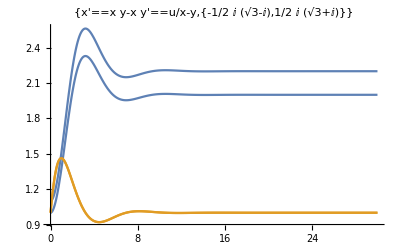

```mathematica
Show[DPlot[circFBL,1,2,1],DPlot[circFBL,1,2.2,1.1]]
```

```mathematica
TableForm@({{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Length/@{all,Connected,SteadyStateExists,Stable,exactAdapNotTrivial,Complement[allAprox,rFCD],Complement[rFCD,allAprox],Intersection[allAprox,rFCD],rFCD},Round[100. 1/(Length@all)Length/@{all,Connected,SteadyStateExists,Stable,exactAdapNotTrivial,Complement[allAprox,rFCD],Complement[rFCD,allAprox],Intersection[allAprox,rFCD],rFCD},0.001]}ᵀ)
```

All Possible Designs | 531441 | 100.
Connected Circuits | 523584 | 98.522
Steady State Exists | 341184 | 64.2
Steady State is Stable | 82656 | 15.553
Exact Adaptation | 7416 | 1.395
Approximate FCD (But not FCD) | 336 | 0.063
FCD (But not Aproximate FCD) | 108 | 0.02
FCD And Aproximate FCD | 536 | 0.101
All FCD circuits | 644 | 0.121

```mathematica
SeperatedTable=(GatherBy[#,Total@(Abs/@#)&])&/@{all,Connected,SteadyStateExists,Stable,exactAdapNotTrivial,Complement[allAprox,rFCD],Complement[rFCD,allAprox],Intersection[allAprox,rFCD],rFCD};
```

```mathematica
TableForm[Normal@(SparseArray@Select[#,#[[1,2]]>0&]&@(Join@@Table[({i,Total@(Abs/@#[[1]])}-> Length@#)&/@SeperatedTable[[i]],{i,Length@SeperatedTable}])),TableHeadings->{{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Range@12}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
All Possible Designs | 24 | 264 | 1760 | 7920 | 25344 | 59136 | 101376 | 126720 | 112640 | 67584 | 24576 | 4096
Connected Circuits | 0 | 80 | 1056 | 6352 | 23168 | 57216 | 100352 | 126464 | 112640 | 67584 | 24576 | 4096
Steady State Exists | 0 | 0 | 128 | 2816 | 12960 | 36000 | 67328 | 87680 | 76608 | 42432 | 13568 | 1664
Steady State is Stable | 0 | 0 | 0 | 576 | 2880 | 8528 | 16512 | 21808 | 18800 | 10064 | 3136 | 352
Exact Adaptation | 0 | 0 | 0 | 64 | 576 | 1152 | 3312 | 2844 | 3328 | 1736 | 648 | 92
Approximate FCD (But not FCD) | 0 | 0 | 0 | 0 | 16 | 104 | 176 | 40 | 0 | 0 | 0 | 0
FCD (But not Aproximate FCD) | 0 | 0 | 0 | 0 | 16 | 8 | 40 | 20 | 16 | 8 | 0 | 0
FCD And Aproximate FCD | 0 | 0 | 0 | 0 | 16 | 104 | 184 | 124 | 80 | 28 | 0 | 0
All FCD circuits | 0 | 0 | 0 | 0 | 32 | 112 | 224 | 144 | 96 | 36 | 0 | 0

## Natural Circuits

```mathematica
natural = Select[all,(αxx==1 &&αyy==1/.Thread[param->#])&];
```

## Connected Natural Circuits

```mathematica
Length[ConnectedNatural = Select[natural,(((αxu≠ 0 ||αyu≠ 0 ||βxu≠ 0 ||βyu≠ 0 )  && (αxu≠ 0 ||αxy≠ 0 ||βxu≠ 0 ||βxy≠ 0 ||αyx ≠0 || βyx ≠0) &&(αyu≠ 0 ||αyx≠ 0 ||βyu≠ 0 ||βyx≠ 0 ||αxy ≠0 || βxy ≠0))/.Thread[param->#])&]];
```

## Steady State Exists Natural Circuits

```mathematica
Length[SteadyStateExistsNatural = Select[ConnectedNatural,((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy)/.Thread[param->#])≠ 0&]];
```

## Stable Steady State Natural Circuits

There exist T || u such that the system is stable

```mathematica
Length[StableNatural=DeleteCases[SteadyStateExistsNatural,_?(!Refine[(Evaluate[(Det@#>0&&Tr@#<0)&@D[eq,{{x,y}}]//FullSimplify]/.Thread[param->#])/.(s/.Thread[param->#]),{T> 0,u>0}]&)]]
```

28416

## Exact Adaptation Natural Circuits

```mathematica
Length[exactAdapNatural=Select[StableNatural,(-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx)/.Thread[param->#])==0&]];
Length[exactAdapNotTrivialNatural=Select[exactAdapNatural,!(βyu==αyu&&βyx==αyx)&&(αxu!=βxu||αyu!=βyu)/.Thread[param->#]&]];
```

## FCD Natural Circuits

```mathematica
Length[rFCDNatural = Select[exactAdapNotTrivialNatural,((αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)||(αxu-αxx==-1&&βxu-βxx==-1&&αyu-αyx==0&&βyu-βyx==0))/.Thread[param->#]&]];
Length[allAproxNatural = Select[exactAdapNotTrivialNatural,(αyy≠βyy&&((1+αxu==αxx&&1+βxu==βxx&&αyu+βyx==αyx+βyu)||(αxu+αxx==1&&αyu+αyx==βyu+βyx&&βxu+βxx==1)))/.Thread[param->#]&]];
Length[rFCDs1Natural = Select[exactAdapNotTrivialNatural,(αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)/.Thread[param->#]&]];
```

```mathematica
TableForm@({{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Length/@{natural,ConnectedNatural,SteadyStateExistsNatural,StableNatural,exactAdapNotTrivialNatural,Complement[allAproxNatural,rFCDNatural],Complement[rFCDNatural,allAproxNatural],Intersection[allAproxNatural,rFCDNatural],rFCDNatural},Round[100. 1/(Length@all)Length/@{natural,ConnectedNatural,SteadyStateExistsNatural,StableNatural,exactAdapNotTrivialNatural,Complement[allAproxNatural,rFCDNatural],Complement[rFCDNatural,allAproxNatural],Intersection[allAproxNatural,rFCDNatural],rFCDNatural},0.001]}ᵀ)
```

All Possible Designs | 59049 | 11.111
Connected Circuits | 58176 | 10.947
Steady State Exists | 38176 | 7.183
Steady State is Stable | 28416 | 5.347
Exact Adaptation | 2108 | 0.397
Approximate FCD (But not FCD) | 160 | 0.03
FCD (But not Aproximate FCD) | 36 | 0.007
FCD And Aproximate FCD | 232 | 0.044
All FCD circuits | 268 | 0.05

```mathematica
SeperatedTableNatural=(GatherBy[#,Total@(Abs/@#)&])&/@{natural,ConnectedNatural,SteadyStateExistsNatural,StableNatural,exactAdapNotTrivialNatural,Complement[allAproxNatural,rFCDNatural],Complement[rFCDNatural,allAproxNatural],Intersection[allAproxNatural,rFCDNatural],rFCDNatural};
```

```mathematica
TableForm[Normal@(SparseArray@Select[#,#[[1,2]]>0&]&@(Join@@Table[({i,Total@(Abs/@#[[1]])}-> Length@#)&/@SeperatedTableNatural[[i]],{i,Length@SeperatedTableNatural}])),TableHeadings->{{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Range@12}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
All Possible Designs | 0 | 1 | 20 | 180 | 960 | 3360 | 8064 | 13440 | 15360 | 11520 | 5120 | 1024
Connected Circuits | 0 | 0 | 0 | 80 | 736 | 3088 | 7872 | 13376 | 15360 | 11520 | 5120 | 1024
Steady State Exists | 0 | 0 | 0 | 80 | 512 | 2080 | 5440 | 9360 | 10384 | 7152 | 2752 | 416
Steady State is Stable | 0 | 0 | 0 | 80 | 512 | 1888 | 4464 | 7072 | 7376 | 4880 | 1856 | 288
Exact Adaptation | 0 | 0 | 0 | 0 | 48 | 200 | 720 | 864 | 1120 | 760 | 316 | 64
Approximate FCD (But not FCD) | 0 | 0 | 0 | 0 | 8 | 40 | 80 | 32 | 0 | 0 | 0 | 0
FCD (But not Aproximate FCD) | 0 | 0 | 0 | 0 | 0 | 0 | 16 | 8 | 8 | 4 | 0 | 0
FCD And Aproximate FCD | 0 | 0 | 0 | 0 | 8 | 40 | 84 | 52 | 32 | 16 | 0 | 0
All FCD circuits | 0 | 0 | 0 | 0 | 8 | 40 | 100 | 60 | 40 | 20 | 0 | 0

## Transcriptional Circuits

```mathematica
transcriptional = Select[all,(αxx==1 &&αyy==1&&αxu==0&&αxy==0&&αyu==0&&αyx==0/.Thread[param->#])&];
```

## Connected Transcriptional Circuits

```mathematica
Length[ConnectedTrans = Select[transcriptional,(((αxu≠ 0 ||αyu≠ 0 ||βxu≠ 0 ||βyu≠ 0 )  && (αxu≠ 0 ||αxy≠ 0 ||βxu≠ 0 ||βxy≠ 0 ||αyx ≠0 || βyx ≠0) &&(αyu≠ 0 ||αyx≠ 0 ||βyu≠ 0 ||βyx≠ 0 ||αxy ≠0 || βxy ≠0))/.Thread[param->#])&]];
```

## Steady State Exists Transcriptional Circuits

```mathematica
Length[SteadyStateExistsTrans = Select[ConnectedTrans,((αxy-βxy) (αyx-βyx)-(αxx-βxx) (αyy-βyy)/.Thread[param->#])≠ 0&]];
```

## Stable Steady State Transcriptional Circuits

There exist T || u That the system is stable

```mathematica
Length[StableTrans=DeleteCases[SteadyStateExistsTrans,_?(!Refine[(Evaluate[(Det@#>0&&Tr@#<0)&@D[eq,{{x,y}}]//FullSimplify]/.Thread[param->#])/.(s/.Thread[param->#]),{T> 0,u>0}]&)]]
```

320

## Exact Adaptation Transcriptional Circuits

```mathematica
Length[exactAdapTrans=Select[StableTrans,(-(αxx-βxx) (αyu-βyu)+(αxu-βxu) (αyx-βyx)/.Thread[param->#])==0&]];
Length[exactAdapNotTrivialTrans=Select[exactAdapTrans,!(βyu==αyu&&βyx==αyx)&&(αxu!=βxu||αyu!=βyu)/.Thread[param->#]&]];
```

## FCD Transcriptional Circuits

```mathematica
Length[rFCDTrans = Select[exactAdapNotTrivialTrans,((αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)||(αxu-αxx==-1&&βxu-βxx==-1&&αyu-αyx==0&&βyu-βyx==0))/.Thread[param->#]&]];
Length[allAproxTrans = Select[exactAdapNotTrivialTrans,(αyy≠βyy&&((1+αxu==αxx&&1+βxu==βxx&&αyu+βyx==αyx+βyu)||(αxu+αxx==1&&αyu+αyx==βyu+βyx&&βxu+βxx==1)))/.Thread[param->#]&]];
Length[rFCDs1Trans = Select[exactAdapNotTrivialTrans,(αxu+αxx==1&&βxu+βxx==1&&αyu+αyx==0&&βyu+βyx==0)/.Thread[param->#]&]];
```

```mathematica
TableForm@({{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Length/@{transcriptional,ConnectedTrans,SteadyStateExistsTrans,StableTrans,exactAdapNotTrivialTrans,Complement[allAproxTrans,rFCDTrans],Complement[rFCDTrans,allAproxTrans],Intersection[allAproxTrans,rFCDTrans],rFCDTrans},Round[100. 1/(Length@all)Length/@{transcriptional,ConnectedTrans,SteadyStateExistsTrans,StableTrans,exactAdapNotTrivialTrans,Complement[allAproxTrans,rFCDTrans],Complement[rFCDTrans,allAproxTrans],Intersection[allAproxTrans,rFCDTrans],rFCDTrans},0.001]}ᵀ)
```

All Possible Designs | 729 | 0.137
Connected Circuits | 612 | 0.115
Steady State Exists | 416 | 0.078
Steady State is Stable | 320 | 0.06
Exact Adaptation | 32 | 0.006
Approximate FCD (But not FCD) | 0 | 0.
FCD (But not Aproximate FCD) | 4 | 0.001
FCD And Aproximate FCD | 28 | 0.005
All FCD circuits | 32 | 0.006

```mathematica
SeperatedTableTrans=(GatherBy[#,Total@(Abs/@#)&])&/@{transcriptional,ConnectedTrans,SteadyStateExistsTrans,StableTrans,exactAdapNotTrivialTrans,Complement[allAproxTrans,rFCDTrans],Complement[rFCDTrans,allAproxTrans],Intersection[allAproxTrans,rFCDTrans],rFCDTrans};
```

```mathematica
TableForm[Normal@(SparseArray@Select[#,#[[1,2]]>0&]&@(Join@@Table[({i,Total@(Abs/@#[[1]])}-> Length@#)&/@SeperatedTableTrans[[i]],{i,Length@SeperatedTableNatural}])),TableHeadings->{{"All Possible Designs","Connected Circuits","Steady State Exists","Steady State is Stable","Exact Adaptation","Approximate FCD (But not FCD)","FCD (But not Aproximate FCD)","FCD And Aproximate FCD","All FCD circuits"},Range@12}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
All Possible Designs | 0 | 1 | 12 | 60 | 160 | 240 | 192 | 64
Connected Circuits | 0 | 0 | 0 | 20 | 112 | 224 | 192 | 64
Steady State Exists | 0 | 0 | 0 | 20 | 64 | 124 | 144 | 64
Steady State is Stable | 0 | 0 | 0 | 20 | 64 | 108 | 96 | 32
Exact Adaptation | 0 | 0 | 0 | 0 | 4 | 12 | 16 | 0
Approximate FCD (But not FCD) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
FCD (But not Aproximate FCD) | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0
FCD And Aproximate FCD | 0 | 0 | 0 | 0 | 4 | 12 | 12 | 0
All FCD circuits | 0 | 0 | 0 | 0 | 4 | 12 | 16 | 0

Plot the circuits:

```mathematica
arrows={#[[3]]->#[[2]],ToExpression@#[[1]] ToExpression@StringJoin@#}&@(Characters[ToString[#]])&/@param;
coordi={"x"->{0,0},"y"->{1,0},"u"->{1/2,√3/2}};
h=Graphics[Line[{{-0,1/2},{0,0},{-0,-1/2}}]];
ah={Arrowheads[{{.06}}],Arrowheads[{{Automatic,Automatic,h}}]};
ArrowsStyleRule={
{α}->{{Dashed,Darker@Red,ah[[2]]}},
{-α}->{{Dashed,Darker@Blue,ah[[1]]}},
{β}->{{Dashing[1],Darker@Blue,ah[[1]]}},
{-β}->{{Dashing[1],Darker@Red,ah[[2]]}},
{α,β}->{{Dashed,Darker@Red,ah[[2]]},{Dashing[1],Darker@Blue,ah[[1]]}},{-α,-β}->{{Dashed,Darker@Blue,ah[[1]]},{Dashing[1],Darker@Red,ah[[2]]}},
{α,-β}->{{Dashed,Darker@Red,ah[[2]]},{Dashing[1],Darker@Red,ah[[2]]}},{-α,β}->{{Dashed,Darker@Blue,ah[[1]]},{Dashing[1],Darker@Blue,ah[[1]]}}};
vertexes=Join[{EdgeForm[Black],Black,Disk[{1/2,√3/2},.1],Text[Style["u",White,12],{1/2,√3/2}]},
{EdgeForm[Black],GrayLevel[.5],Disk[{0,0},.1],Text[Style["x",White,12],{0,0}]},
{EdgeForm[Black],White,Disk[{1,0},.1],Text[Style["y",Black,12],{1,0}]}];
th[x_]:=Thread[param->x]
NNN[d_]:=Module[{p=d},
p[[8]]=If[p[[8]]==-1,-1,0];
p[[12]]=If[p[[12]]==-1,-1,0];
Framed@Graphics[Flatten[{Thick,({Sort@DeleteCases[#,Arrow[__]]/.ArrowsStyleRule,Cases[#,Arrow[__]]}ᵀ&@#[[;;,2]])&/@GatherBy[Flatten[{#,{Rule@@(Switch[#,{0.5,0.9},"u",{0.,0.},"x",{1.,0.},"y"]&/@Round[#[[1,{1,-1}]],.1]),#}&/@Cases[GraphPlot[#[[;;,1]],
EdgeRenderingFunction->(Flatten[{Thick,Arrow[#1,.15]}]&),
VertexCoordinateRules->coordi],Arrow[__],∞]}&@DeleteCases[arrows/.th[p],{_,0}],1],First],vertexes,If[d[[8]]==0,{Black,Dashing[1],Arrowheads[{{Automatic,Automatic,Graphics[Disk[{0,0},.25]]}}],Arrow[{{0,0},{-.3,-.3/√3}},.1]},{}],If[d[[12]]==0,{Black,Dashing[1],Arrowheads[{{Automatic,Automatic,Graphics[Disk[{0,0},.25]]}}],Arrow[{{1,0},{1.3,-.3/√3}},.1]},{}]}](*,*)(*PlotLabel->Framed@TableForm[Thread[{x',y'}==EQP[d,T]]],*),ImageSize->200,ImageMargins->1]]
```

```mathematica
s2 = Table[ TableForm[{Framed@TableForm@Thread[{dx/dt,dy/dt}==EQP[rFCD[[i]],T]],NNN[rFCD[[i]]]},TableAlignments->Center],{i,644}];
```

```mathematica
S2=(Partition[s2,4]//Grid);
```

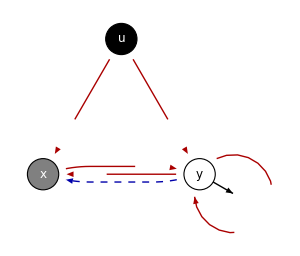
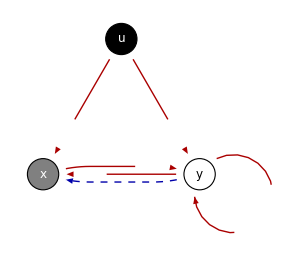
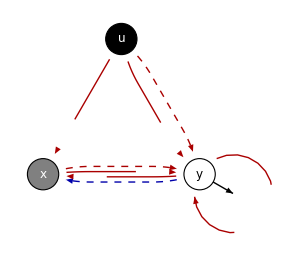
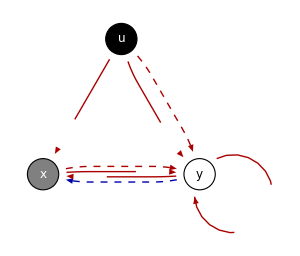
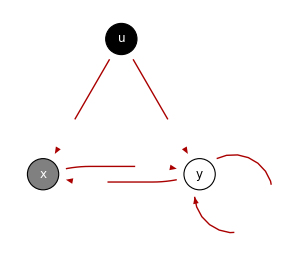
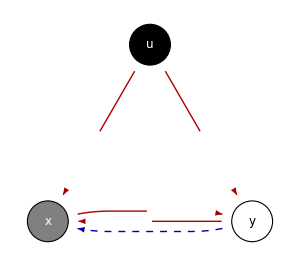
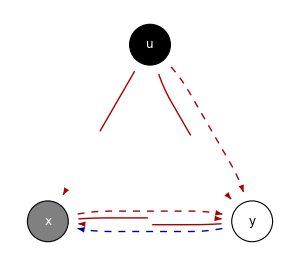
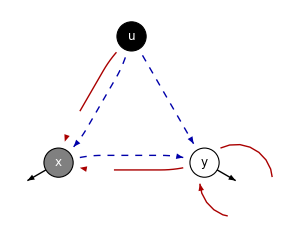
dx/dt==1/(u y)-x/y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1/(u x y)-u x y)
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T (-1/(u x)+1/y)
-Graphics-
dx/dt==-1/u+1/(u y)
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (-1/(u x)+1/y)
-Graphics-
dx/dt==1/(u y)-x/y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (1/y-1/(u x y))
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (1/y-1/(u x y))
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T (1-y/(u x))
-Graphics-
dx/dt==1/(u y)-x/y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (1-u x y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (1-1/(u x))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (1-y/(u x))
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (1-1/(u x y))
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (1-1/(u x))
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (y-y/(u x))
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x)+y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (y-y/(u x))
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T ((u x)/y-y/(u x))
-Graphics-
dx/dt==-1/u+1/(u y)
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T ((u x)/y-y/(u x))
-Graphics-
dx/dt==1/(u y)-y/u
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T ((u x)/y-y/(u x))
-Graphics-
dx/dt==1/(u y)-x/y
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1/(u x y)+(u x)/y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1/y+(u x)/y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T ((u x)/y-y)
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x y)+(u x)/y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1/y+(u x)/y)
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==-1/u+1/(u y)
dy/dt==T (u x-y)
-Graphics-
dx/dt==1/(u y)-y/u
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==1/(u y)-y/u
dy/dt==T (u x-y)
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==1/(u y)-x/y
dy/dt==T (u x-y)
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T (u x-1/(u x y))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1/(u x)+u x)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1+u x)
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T (u x-y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (u x-1/(u x y))
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x)+u x)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (u x-y/(u x))
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (u x-1/y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1+u x)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (u x-y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-1/(u x)+u x y)
-Graphics-
dx/dt==-x+1/(u y)
dy/dt==T (-y/(u x)+u x y)
-Graphics- | dx/dt==-x+1/(u y)
dy/dt==T (-y+u x y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x y)+u x y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1/(u x)+u x y)
-Graphics-
dx/dt==1/(u y)-x y
dy/dt==T (-y/(u x)+u x y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-1+u x y)
-Graphics- | dx/dt==1/(u y)-x y
dy/dt==T (-y+u x y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (-1+1/(u x y))
-Graphics-
dx/dt==1/u-1/(u y)
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (-1/y+1/(u x y))
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/(u x y)-(u x)/y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (-u x+1/(u x y))
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==1/u-x
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (-u x+1/(u x y))
-Graphics-
dx/dt==1/u-x
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (1/(u x)-u x y)
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (-1+1/(u x))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/(u x)-(u x)/y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/(u x)-u x)
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (-y+y/(u x))
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (-u x+y/(u x))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (y/(u x)-u x y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (1/y-u x y)
-Graphics-
dx/dt==1/u-y/u
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==1/u-y/u
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/y-(u x)/y)
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (1/y-y/(u x))
-Graphics-
dx/dt==1/u-x
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (1/y-1/(u x y))
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-1/(u x)+1/y)
-Graphics-
dx/dt==1/u-x y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==1/u-x y
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==1/u-1/(u y)
dy/dt==T (1-u x y)
-Graphics- | dx/dt==1/u-y/u
dy/dt==T (1-y/(u x))
-Graphics-
dx/dt==1/u-x/y
dy/dt==T (1-u x)
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (1-u x y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==1/u-x
dy/dt==T (1-u x y)
-Graphics-
dx/dt==1/u-x y
dy/dt==T (1-1/(u x))
-Graphics- | dx/dt==1/u-x y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==1/u-x/y
dy/dt==T (y-u x y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (y-y/(u x))
-Graphics-
dx/dt==1/u-y/u
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/u-y/u
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==1/u-y/u
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==1/u-y/u
dy/dt==T ((u x)/y-y)
-Graphics-
dx/dt==1/u-x/y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/u-x
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==1/u-x
dy/dt==T (-1+(u x)/y)
-Graphics-
dx/dt==1/u-x
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-1/(u x y)+(u x)/y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T ((u x)/y-y/(u x))
-Graphics-
dx/dt==1/u-x y
dy/dt==T (-1/y+(u x)/y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==1/u-y/u
dy/dt==T (u x-y/(u x))
-Graphics-
dx/dt==1/u-y/u
dy/dt==T (u x-y)
-Graphics- | dx/dt==1/u-x
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==1/u-x
dy/dt==T (u x-y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (u x-1/(u x y))
-Graphics-
dx/dt==1/u-x y
dy/dt==T (-1/(u x)+u x)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-1+u x)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (u x-y)
-Graphics-
dx/dt==1/u-x y
dy/dt==T (-1/(u x)+u x y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-y/(u x)+u x y)
-Graphics- | dx/dt==1/u-x y
dy/dt==T (-y+u x y)
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (-1+1/(u x y))
-Graphics-
dx/dt==-1/(u y)+y/u
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (-1+1/(u x y))
-Graphics-
dx/dt==-1/u+y/u
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-1/y+1/(u x y))
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x y)-(u x)/y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-u x+1/(u x y))
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-1/y+1/(u x y))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/(u x y)-y)
-Graphics-
dx/dt==-x+y/u
dy/dt==T (1/(u x y)-(u x)/y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (-1+1/(u x y))
-Graphics-
dx/dt==y/u-x y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (1/(u x)-y)
-Graphics-
dx/dt==-1/(u y)+y/u
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x)-1/y)
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (-1+1/(u x))
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x)-(u x)/y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/(u x)-u x)
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-1+1/(u x))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/(u x)-(u x)/y)
-Graphics-
dx/dt==-x+y/u
dy/dt==T (1/(u x)-u x)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1/(u x)-u x y)
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (-1+y/(u x))
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-y+y/(u x))
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-(u x)/y+y/(u x))
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-u x+y/(u x))
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (y/(u x)-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-y+y/(u x))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-u x+y/(u x))
-Graphics- | dx/dt==-x+y/u
dy/dt==T (y/(u x)-u x y)
-Graphics-
dx/dt==-1/(u y)+y/u
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-1/u+y/u
dy/dt==T (1/y-u x y)
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (1/y-(u x)/y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/y-y/(u x))
-Graphics-
dx/dt==-x+y/u
dy/dt==T (1/y-(u x)/y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (-1/(u x)+1/y)
-Graphics-
dx/dt==y/u-x y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==y/u-x y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1/y-u x y)
-Graphics- | dx/dt==-1/(u y)+y/u
dy/dt==T (1-u x y)
-Graphics-
dx/dt==-1/u+y/u
dy/dt==T (1-u x y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1-(u x)/y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1-u x)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (1-u x y)
-Graphics-
dx/dt==-x+y/u
dy/dt==T (1-u x)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (1-u x y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==y/u-x y
dy/dt==T (1-u x y)
-Graphics-
dx/dt==-x/y+y/u
dy/dt==T (-u x+y)
-Graphics- | dx/dt==-x/y+y/u
dy/dt==T (y-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T (y-u x y)
-Graphics- | dx/dt==-x+y/u
dy/dt==T ((u x)/y-y)
-Graphics-
dx/dt==y/u-x y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==y/u-x y
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==y/u-x y
dy/dt==T ((u x)/y-y)
-Graphics-
dx/dt==y/u-x y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==y/u-x y
dy/dt==T (u x-y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==-x+x/y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==-x+x/y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==-x+x/y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==x/y-x y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==x/y-x y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==x/y-x y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==-u+x/y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==x/y-u y
dy/dt==T (-1+x/(u y))
-Graphics-
dx/dt==x/y-u y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==x/y-u y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (x/u-(u y)/x)
-Graphics-
dx/dt==x/y-x y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==-u+x/y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==x/y-u y
dy/dt==T (x/u-y)
-Graphics-
dx/dt==x/y-u y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==x/y-y/u
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (1/y-y/(u x))
-Graphics-
dx/dt==-x+x/y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (1/y-y/(u x))
-Graphics-
dx/dt==x/y-x y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==x/y-u y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==x/y-y/u
dy/dt==T (1-y/(u x))
-Graphics-
dx/dt==-x+x/y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==-x+x/y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==x/y-x y
dy/dt==T (1-(u y)/x)
-Graphics-
dx/dt==x/y-u y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==-1/u+x/y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==x/y-y/u
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==x/y-y/u
dy/dt==T ((u x)/y-y/(u x))
-Graphics-
dx/dt==x/y-y/u
dy/dt==T (-1+(u x)/y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==-x+x/y
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==-x+x/y
dy/dt==T (-1+(u x)/y)
-Graphics-
dx/dt==-x+x/y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==x/y-x y
dy/dt==T (-1+(u x)/y)
-Graphics-
dx/dt==x/y-x y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==-1/u+x/y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==x/y-y/u
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==x/y-y/u
dy/dt==T (u x-y)
-Graphics-
dx/dt==-x+x/y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==-x+x/y
dy/dt==T (u x-y)
-Graphics- | dx/dt==x/y-x y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==x/y-x y
dy/dt==T (u x-y)
-Graphics-
dx/dt==x-1/(u y)
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==x-x/y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==x-x/y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==x-x/y
dy/dt==T (-u x+1/(u x y))
-Graphics-
dx/dt==x-x/y
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==x-1/(u y)
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==x-x/y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==x-x/y
dy/dt==T (1/(u x)-u x y)
-Graphics-
dx/dt==x-x y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==x-x y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==x-x y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==x-x y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics-
dx/dt==x-u y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==x-x y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==x-x y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==x-u y
dy/dt==T (x/u-(u y)/x)
-Graphics-
dx/dt==x-x/y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==x-x/y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==x-x/y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==x-x/y
dy/dt==T (1/y-u x y)
-Graphics-
dx/dt==x-x y
dy/dt==T (-1/(u x)+1/y)
-Graphics- | dx/dt==x-x y
dy/dt==T (1/y-y/(u x))
-Graphics- | dx/dt==x-x y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==x-x y
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==x-x/y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==x-x/y
dy/dt==T (1-u x y)
-Graphics- | dx/dt==x-x y
dy/dt==T (1-y/(u x))
-Graphics- | dx/dt==x-x y
dy/dt==T (1-(u y)/x)
-Graphics-
dx/dt==x-x/y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==x-x/y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==x-x/y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==x-x/y
dy/dt==T (u/(x y)-y)
-Graphics-
dx/dt==x-u/y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==x-x/y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==x-x/y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==x-u/y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==x-y/u
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==x-x y
dy/dt==T (-1/(u x)+(u x)/y)
-Graphics- | dx/dt==x-x y
dy/dt==T ((u x)/y-y/(u x))
-Graphics- | dx/dt==x-x y
dy/dt==T (-1+(u x)/y)
-Graphics-
dx/dt==x-x y
dy/dt==T ((u x)/y-y)
-Graphics- | dx/dt==x-y/u
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==x-x y
dy/dt==T (u x-y/(u x))
-Graphics- | dx/dt==x-x y
dy/dt==T (u x-y)
-Graphics-
dx/dt==-1/(u y)+x y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==-1/(u y)+x y
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-1/(u y)+x y
dy/dt==T (1/(u x y)-u x y)
-Graphics- | dx/dt==-1/u+x y
dy/dt==T (-u x+1/(u x y))
-Graphics-
dx/dt==-x/y+x y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1/(u x y)-u x y)
-Graphics-
dx/dt==-x+x y
dy/dt==T (-1+1/(u x y))
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/(u x y)-y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (-u x+1/(u x y))
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/(u x y)-u x y)
-Graphics-
dx/dt==-1/(u y)+x y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==-1/(u y)+x y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-1/u+x y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1/(u x)-y)
-Graphics-
dx/dt==-x/y+x y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/(u x)-y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/(u x)-u x y)
-Graphics- | dx/dt==-1/(u y)+x y
dy/dt==T (-u x+1/y)
-Graphics-
dx/dt==-x/y+x y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1/y-u x y)
-Graphics-
dx/dt==-x+x y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-x+x y
dy/dt==T (-u x+1/y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (1/y-u x y)
-Graphics-
dx/dt==-u/y+x y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-1/(u y)+x y
dy/dt==T (1-u x y)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (1-u x y)
-Graphics-
dx/dt==-x+x y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==-x+x y
dy/dt==T (1-u x y)
-Graphics- | dx/dt==-u/y+x y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==-x/y+x y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==-x+x y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-x+x y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-x+x y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-u/y+x y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==-u/y+x y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-u/y+x y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-u+x y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==-x/y+x y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==-x/y+x y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==-x+x y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==-x+x y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==-u/y+x y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==-u/y+x y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==-u+x y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==u/y-x/y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-1/y+x/(u y))
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-1+x/(u y))
-Graphics-
dx/dt==-x+u/y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-u/(x y)+x/(u y))
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==-x+u/y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics-
dx/dt==u/y-x y
dy/dt==T (-1/y+x/(u y))
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u/y-x y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-u/(x y)+x/(u y))
-Graphics-
dx/dt==u/y-x y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u/y-x y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==-u+u/y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==-u+u/y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==-u+u/y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==-u+u/y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==u/y-u y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u/y-u y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==u/y-u y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u/y-u y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (x/u-(u y)/x)
-Graphics-
dx/dt==-x+u/y
dy/dt==T (-1+x/u)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (x/u-u/(x y))
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-u/x+x/u)
-Graphics-
dx/dt==-x+u/y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (x/u-1/y)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-1+x/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (x/u-y)
-Graphics-
dx/dt==u/y-x y
dy/dt==T (x/u-u/(x y))
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-u/x+x/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==-u+u/y
dy/dt==T (x/u-y)
-Graphics-
dx/dt==-u+u/y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==u/y-u y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==u/y-u y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-y+(x y)/u)
-Graphics-
dx/dt==-x+u/y
dy/dt==T (-u/x+(x y)/u)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-(u y)/x+(x y)/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-1+(x y)/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-y+(x y)/u)
-Graphics-
dx/dt==u/y-x y
dy/dt==T (-u/(x y)+(x y)/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-u/x+(x y)/u)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (-(u y)/x+(x y)/u)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (-x/u+1/y)
-Graphics-
dx/dt==u/y-x/y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (1/y-(x y)/u)
-Graphics-
dx/dt==-x+u/y
dy/dt==T (1/y-u/(x y))
-Graphics- | dx/dt==-x+u/y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (1/y-u/(x y))
-Graphics-
dx/dt==u/y-x y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==-u+u/y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==-u+u/y
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==u/y-u y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u/y-u y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (1-(u y)/x)
-Graphics-
dx/dt==-x+u/y
dy/dt==T (1-u/x)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (1-u/(x y))
-Graphics- | dx/dt==u/y-x y
dy/dt==T (1-u/x)
-Graphics-
dx/dt==u/y-x y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==-u+u/y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==u/y-u y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (y-(u y)/x)
-Graphics-
dx/dt==u/y-x y
dy/dt==T (-u/x+y)
-Graphics- | dx/dt==u/y-x y
dy/dt==T (y-(u y)/x)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics-
dx/dt==u/y-x/y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-x+u/y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==u/y-x/y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==u/y-x/y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==u-x/y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==u-x
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u-x
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==u-x
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u-x
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==u-x y
dy/dt==T (-1/y+x/(u y))
-Graphics- | dx/dt==u-x y
dy/dt==T (-1+x/(u y))
-Graphics-
dx/dt==u-x y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==u-x y
dy/dt==T (-u/(x y)+x/(u y))
-Graphics- | dx/dt==u-x y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u-x y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics-
dx/dt==u-u y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u-u y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==u-u y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u-u y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics-
dx/dt==u-x
dy/dt==T (x/u-y)
-Graphics- | dx/dt==u-x
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==u-x y
dy/dt==T (-1+x/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (x/u-y)
-Graphics-
dx/dt==u-x y
dy/dt==T (x/u-u/(x y))
-Graphics- | dx/dt==u-x y
dy/dt==T (-u/x+x/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==u-u y
dy/dt==T (x/u-y)
-Graphics-
dx/dt==u-u y
dy/dt==T (x/u-(u y)/x)
-Graphics- | dx/dt==u-x y
dy/dt==T (-y+(x y)/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (-u/x+(x y)/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (-(u y)/x+(x y)/u)
-Graphics-
dx/dt==u-x/y
dy/dt==T (1/y-x/(u y))
-Graphics- | dx/dt==u-x/y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==u-x/y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u-x/y
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==u-x
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==u-x
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u-x
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u-x
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==u-x y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (1/y-u/(x y))
-Graphics- | dx/dt==u-x y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u-x y
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==u-u/y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==u-u/y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u-u y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u-u y
dy/dt==T (1/y-(u y)/x)
-Graphics-
dx/dt==u-x/y
dy/dt==T (1-x/u)
-Graphics- | dx/dt==u-x/y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==u-x
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==u-x
dy/dt==T (1-(u y)/x)
-Graphics-
dx/dt==u-x y
dy/dt==T (1-u/x)
-Graphics- | dx/dt==u-x y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==u-u/y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==u-u y
dy/dt==T (1-(u y)/x)
-Graphics-
dx/dt==u-x/y
dy/dt==T (y-(x y)/u)
-Graphics- | dx/dt==u-x y
dy/dt==T (y-(u y)/x)
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/(x y)-x/(u y))
-Graphics- | dx/dt==u-x/y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==u-x/y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==u-x/y
dy/dt==T (-1/y+u/(x y))
-Graphics- | dx/dt==u-x/y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/(x y)-y)
-Graphics-
dx/dt==u-x
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==u-x
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==u-x
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==u-x
dy/dt==T (u/(x y)-y)
-Graphics-
dx/dt==u-x y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==u-u/y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==u-u/y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==u-u/y
dy/dt==T (-1+u/(x y))
-Graphics-
dx/dt==u-u/y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/x-x/(u y))
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/x-x/u)
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==u-x/y
dy/dt==T (-1+u/x)
-Graphics- | dx/dt==u-x/y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==u-x
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==u-x
dy/dt==T (u/x-y)
-Graphics-
dx/dt==u-u/y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==u-u/y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==u-x/y
dy/dt==T (-x/u+(u y)/x)
-Graphics- | dx/dt==u-x/y
dy/dt==T ((u y)/x-(x y)/u)
-Graphics-
dx/dt==u-x/y
dy/dt==T (-y+(u y)/x)
-Graphics- | dx/dt==-x+u y
dy/dt==T (x/(u y)-y)
-Graphics- | dx/dt==u y-x y
dy/dt==T (-1+x/(u y))
-Graphics- | dx/dt==u y-x y
dy/dt==T (x/(u y)-y)
-Graphics-
dx/dt==u y-x y
dy/dt==T (-u/x+x/(u y))
-Graphics- | dx/dt==u y-x y
dy/dt==T (x/(u y)-(u y)/x)
-Graphics- | dx/dt==u y-x y
dy/dt==T (x/u-y)
-Graphics- | dx/dt==u y-x y
dy/dt==T (x/u-(u y)/x)
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (1/y-x/(u y))
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (1/y-x/(u y))
-Graphics-
dx/dt==-x+u y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-x+u y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==u y-x y
dy/dt==T (-x/u+1/y)
-Graphics-
dx/dt==u y-x y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==u y-x y
dy/dt==T (-u/x+1/y)
-Graphics- | dx/dt==u y-x y
dy/dt==T (1/y-(u y)/x)
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (-x/u+1/y)
-Graphics-
dx/dt==-u/y+u y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-u+u y
dy/dt==T (-x/u+1/y)
-Graphics- | dx/dt==-u+u y
dy/dt==T (1/y-(x y)/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (1-x/(u y))
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (1-x/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (1-x/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (1-(x y)/u)
-Graphics-
dx/dt==u y-x y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==u y-x y
dy/dt==T (1-(u y)/x)
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (1-(x y)/u)
-Graphics- | dx/dt==-u+u y
dy/dt==T (1-(x y)/u)
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (-x/u+y)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (y-(x y)/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (y-(x y)/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (u/(x y)-x/(u y))
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-1/y+u/(x y))
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-1+u/(x y))
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/(x y)-x/(u y))
-Graphics- | dx/dt==-x+u y
dy/dt==T (-x/u+u/(x y))
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics-
dx/dt==-x+u y
dy/dt==T (-1/y+u/(x y))
-Graphics- | dx/dt==-x+u y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==u y-x y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==u y-x y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==u y-x y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==u y-x y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==-u/y+u y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-u+u y
dy/dt==T (-x/u+u/(x y))
-Graphics-
dx/dt==-u+u y
dy/dt==T (u/(x y)-(x y)/u)
-Graphics- | dx/dt==-u+u y
dy/dt==T (-1+u/(x y))
-Graphics- | dx/dt==-u+u y
dy/dt==T (u/(x y)-y)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (u/x-x/(u y))
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (u/x-x/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (u/x-1/y)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-1+u/x)
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/x-x/(u y))
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/x-x/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/x-(x y)/u)
-Graphics-
dx/dt==-x+u y
dy/dt==T (-1+u/x)
-Graphics- | dx/dt==-x+u y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==u y-x y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==u y-x y
dy/dt==T (u/x-y)
-Graphics-
dx/dt==-u/y+u y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==-u/y+u y
dy/dt==T (u/x-y)
-Graphics- | dx/dt==-u+u y
dy/dt==T (u/x-(x y)/u)
-Graphics- | dx/dt==-u+u y
dy/dt==T (u/x-y)
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (-x/(u y)+(u y)/x)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-x/u+(u y)/x)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T ((u y)/x-(x y)/u)
-Graphics- | dx/dt==-x/y+u y
dy/dt==T (-1+(u y)/x)
-Graphics-
dx/dt==-x/y+u y
dy/dt==T (-y+(u y)/x)
-Graphics- | dx/dt==-x+u y
dy/dt==T (-x/u+(u y)/x)
-Graphics- | dx/dt==-x+u y
dy/dt==T ((u y)/x-(x y)/u)
-Graphics- | dx/dt==-x+u y
dy/dt==T (-y+(u y)/x)
-Graphics-
 |  |  |  |

```mathematica
S2
```

Find the symmetry:

```mathematica
(symU =Gather[rFCD,(#1==({-βyu,βyy,βyz,-βzu,βzy,βzz,-αyu,αyy,αyz,-αzu,αzy,αzz}/.Thread[param->#2])&)]);
```

```mathematica
(symY=Select[Gather[rFCD,(({αyu,2-αyy,αyz,βzu,-βzy,βzz,βyu,2-βyy,βyz,αzu,-αzy,αzz}/.Thread[param->#1])==#2&)],Length@#>1&]);
```

```mathematica
syFCD={{0,1,-1,-1,1,-1,0,1,0,0,0,0},{0,1,-1,-1,1,-1,0,1,0,0,0,1},{0,1,-1,-1,1,-1,0,1,0,1,-1,0},{0,1,-1,-1,1,-1,0,1,0,1,-1,1},{0,1,-1,-1,1,-1,0,1,1,0,0,0},{0,1,-1,-1,1,-1,0,1,1,0,0,1},{0,1,-1,-1,1,-1,0,1,1,1,-1,0},{0,1,-1,-1,1,-1,0,1,1,1,-1,1},{0,1,-1,-1,1,-1,1,0,0,1,-1,0},{0,1,-1,-1,1,-1,1,0,1,0,0,0},{0,1,-1,-1,1,-1,1,0,1,1,-1,0},{0,1,-1,-1,1,-1,1,0,1,1,-1,1},{0,1,-1,-1,1,0,0,1,0,0,0,1},{0,1,-1,-1,1,0,0,1,0,1,-1,1},{0,1,-1,-1,1,0,0,1,1,0,0,1},{0,1,-1,-1,1,0,0,1,1,1,-1,1},{0,1,-1,-1,1,0,1,0,0,1,-1,1},{0,1,-1,-1,1,0,1,0,1,0,0,1},{0,1,-1,-1,1,0,1,0,1,1,-1,1},{0,1,-1,0,0,-1,0,1,0,1,-1,0},{0,1,-1,0,0,-1,0,1,0,1,-1,1},{0,1,-1,0,0,-1,0,1,1,1,-1,0},{0,1,-1,0,0,-1,0,1,1,1,-1,1},{0,1,-1,0,0,-1,1,0,1,1,-1,0},{0,1,-1,0,0,0,0,1,0,1,-1,1},{0,1,-1,0,0,0,0,1,1,1,-1,1},{0,1,-1,0,0,0,1,0,1,1,-1,1},{0,1,0,-1,1,-1,0,1,1,0,0,0},{0,1,0,-1,1,-1,0,1,1,0,0,1},{0,1,0,-1,1,-1,0,1,1,1,-1,0},{0,1,0,-1,1,-1,0,1,1,1,-1,1},{0,1,0,-1,1,-1,1,0,1,1,-1,0},{0,1,0,-1,1,0,0,1,1,0,0,1},{0,1,0,-1,1,0,0,1,1,1,-1,1},{0,1,0,-1,1,0,1,0,1,1,-1,1},{0,1,0,0,0,-1,0,1,-1,-1,1,0},{0,1,0,0,0,-1,0,1,-1,-1,1,1},{0,1,0,0,0,-1,0,1,1,1,-1,0},{0,1,0,0,0,-1,0,1,1,1,-1,1},{0,1,0,0,0,0,0,1,-1,-1,1,1},{0,1,0,0,0,0,0,1,1,1,-1,1},{0,1,0,1,-1,-1,0,1,-1,-1,1,0},{0,1,0,1,-1,-1,0,1,-1,-1,1,1},{0,1,0,1,-1,-1,0,1,-1,0,0,0},{0,1,0,1,-1,-1,0,1,-1,0,0,1},{0,1,0,1,-1,-1,1,0,-1,-1,1,0},{0,1,0,1,-1,0,0,1,-1,-1,1,1},{0,1,0,1,-1,0,0,1,-1,0,0,1},{0,1,0,1,-1,0,1,0,-1,-1,1,1},{0,1,1,0,0,-1,0,1,-1,-1,1,0},{0,1,1,0,0,-1,0,1,-1,-1,1,1},{0,1,1,0,0,-1,0,1,0,-1,1,0},{0,1,1,0,0,-1,0,1,0,-1,1,1},{0,1,1,0,0,-1,1,0,-1,-1,1,0},{0,1,1,0,0,0,0,1,-1,-1,1,1},{0,1,1,0,0,0,0,1,0,-1,1,1},{0,1,1,0,0,0,1,0,-1,-1,1,1},{0,1,1,1,-1,-1,0,1,-1,-1,1,0},{0,1,1,1,-1,-1,0,1,-1,-1,1,1},{0,1,1,1,-1,-1,0,1,-1,0,0,0},{0,1,1,1,-1,-1,0,1,-1,0,0,1},{0,1,1,1,-1,-1,0,1,0,-1,1,0},{0,1,1,1,-1,-1,0,1,0,-1,1,1},{0,1,1,1,-1,-1,0,1,0,0,0,0},{0,1,1,1,-1,-1,0,1,0,0,0,1},{0,1,1,1,-1,-1,1,0,-1,-1,1,0},{0,1,1,1,-1,-1,1,0,-1,-1,1,1},{0,1,1,1,-1,-1,1,0,-1,0,0,0},{0,1,1,1,-1,-1,1,0,0,-1,1,0},{0,1,1,1,-1,0,0,1,-1,-1,1,1},{0,1,1,1,-1,0,0,1,-1,0,0,1},{0,1,1,1,-1,0,0,1,0,-1,1,1},{0,1,1,1,-1,0,0,1,0,0,0,1},{0,1,1,1,-1,0,1,0,-1,-1,1,1},{0,1,1,1,-1,0,1,0,-1,0,0,1},{0,1,1,1,-1,0,1,0,0,-1,1,1},{1,0,-1,-1,1,-1,0,1,-1,0,0,0},{1,0,-1,-1,1,-1,0,1,-1,0,0,1},{1,0,-1,-1,1,-1,0,1,-1,1,-1,0},{1,0,-1,-1,1,-1,0,1,-1,1,-1,1},{1,0,-1,-1,1,-1,0,1,0,0,0,-1},{1,0,-1,-1,1,-1,0,1,0,0,0,0},{1,0,-1,-1,1,-1,0,1,0,0,0,1},{1,0,-1,-1,1,-1,0,1,0,1,-1,-1},{1,0,-1,-1,1,-1,0,1,0,1,-1,0},{1,0,-1,-1,1,-1,0,1,0,1,-1,1},{1,0,-1,-1,1,-1,0,1,1,0,0,-1},{1,0,-1,-1,1,-1,0,1,1,0,0,0},{1,0,-1,-1,1,-1,0,1,1,0,0,1},{1,0,-1,-1,1,-1,0,1,1,1,-1,-1},{1,0,-1,-1,1,-1,0,1,1,1,-1,0},{1,0,-1,-1,1,-1,0,1,1,1,-1,1},{1,0,-1,-1,1,-1,1,0,0,0,0,0},{1,0,-1,-1,1,-1,1,0,0,0,0,1},{1,0,-1,-1,1,-1,1,0,0,1,-1,0},{1,0,-1,-1,1,-1,1,0,0,1,-1,1},{1,0,-1,-1,1,-1,1,0,1,0,0,0},{1,0,-1,-1,1,-1,1,0,1,0,0,1},{1,0,-1,-1,1,-1,1,0,1,1,-1,0},{1,0,-1,-1,1,-1,1,0,1,1,-1,1},{1,0,-1,-1,1,0,0,1,-1,0,0,1},{1,0,-1,-1,1,0,0,1,-1,1,-1,1},{1,0,-1,-1,1,0,0,1,0,0,0,0},{1,0,-1,-1,1,0,0,1,0,0,0,1},{1,0,-1,-1,1,0,0,1,0,1,-1,-1},{1,0,-1,-1,1,0,0,1,0,1,-1,0},{1,0,-1,-1,1,0,0,1,0,1,-1,1},{1,0,-1,-1,1,0,0,1,1,0,0,-1},{1,0,-1,-1,1,0,0,1,1,0,0,0},{1,0,-1,-1,1,0,0,1,1,0,0,1},{1,0,-1,-1,1,0,0,1,1,1,-1,-1},{1,0,-1,-1,1,0,0,1,1,1,-1,0},{1,0,-1,-1,1,0,0,1,1,1,-1,1},{1,0,-1,-1,1,0,1,0,0,0,0,1},{1,0,-1,-1,1,0,1,0,0,1,-1,1},{1,0,-1,-1,1,0,1,0,1,0,0,1},{1,0,-1,-1,1,0,1,0,1,1,-1,1},{1,0,-1,-1,1,1,0,1,0,0,0,1},{1,0,-1,-1,1,1,0,1,0,1,-1,0},{1,0,-1,-1,1,1,0,1,0,1,-1,1},{1,0,-1,-1,1,1,0,1,1,0,0,0},{1,0,-1,-1,1,1,0,1,1,0,0,1},{1,0,-1,-1,1,1,0,1,1,1,-1,-1},{1,0,-1,-1,1,1,0,1,1,1,-1,0},{1,0,-1,-1,1,1,0,1,1,1,-1,1},{1,0,-1,0,0,-1,0,1,-1,-1,1,0},{1,0,-1,0,0,-1,0,1,-1,-1,1,1},{1,0,-1,0,0,-1,0,1,-1,1,-1,0},{1,0,-1,0,0,-1,0,1,-1,1,-1,1},{1,0,-1,0,0,-1,0,1,0,-1,1,1},{1,0,-1,0,0,-1,0,1,0,1,-1,-1},{1,0,-1,0,0,-1,0,1,0,1,-1,0},{1,0,-1,0,0,-1,0,1,0,1,-1,1},{1,0,-1,0,0,-1,0,1,1,1,-1,-1},{1,0,-1,0,0,-1,0,1,1,1,-1,0},{1,0,-1,0,0,-1,0,1,1,1,-1,1},{1,0,-1,0,0,-1,1,0,0,1,-1,0},{1,0,-1,0,0,-1,1,0,0,1,-1,1},{1,0,-1,0,0,-1,1,0,1,1,-1,0},{1,0,-1,0,0,-1,1,0,1,1,-1,1},{1,0,-1,0,0,0,0,1,-1,-1,1,1},{1,0,-1,0,0,0,0,1,-1,1,-1,1},{1,0,-1,0,0,0,0,1,0,1,-1,0},{1,0,-1,0,0,0,0,1,0,1,-1,1},{1,0,-1,0,0,0,0,1,1,1,-1,-1},{1,0,-1,0,0,0,0,1,1,1,-1,0},{1,0,-1,0,0,0,0,1,1,1,-1,1},{1,0,-1,0,0,0,1,0,0,1,-1,1},{1,0,-1,0,0,0,1,0,1,1,-1,1},{1,0,-1,0,0,1,0,1,0,1,-1,1},{1,0,-1,0,0,1,0,1,1,1,-1,0},{1,0,-1,0,0,1,0,1,1,1,-1,1},{1,0,-1,1,-1,-1,0,1,-1,-1,1,0},{1,0,-1,1,-1,-1,0,1,-1,-1,1,1},{1,0,-1,1,-1,-1,0,1,-1,0,0,0},{1,0,-1,1,-1,-1,0,1,-1,0,0,1},{1,0,-1,1,-1,-1,0,1,0,0,0,1},{1,0,-1,1,-1,0,0,1,-1,-1,1,1},{1,0,-1,1,-1,0,0,1,-1,0,0,1},{1,0,0,-1,1,-1,0,1,-1,0,0,1},{1,0,0,-1,1,-1,0,1,0,0,0,0},{1,0,0,-1,1,-1,0,1,0,0,0,1},{1,0,0,-1,1,-1,0,1,0,1,-1,0},{1,0,0,-1,1,-1,0,1,0,1,-1,1},{1,0,0,-1,1,-1,0,1,1,0,0,-1},{1,0,0,-1,1,-1,0,1,1,0,0,0},{1,0,0,-1,1,-1,0,1,1,0,0,1},{1,0,0,-1,1,-1,0,1,1,1,-1,-1},{1,0,0,-1,1,-1,0,1,1,1,-1,0},{1,0,0,-1,1,-1,0,1,1,1,-1,1},{1,0,0,-1,1,-1,1,0,1,0,0,0},{1,0,0,-1,1,-1,1,0,1,0,0,1},{1,0,0,-1,1,-1,1,0,1,1,-1,0},{1,0,0,-1,1,-1,1,0,1,1,-1,1},{1,0,0,-1,1,0,0,1,0,0,0,1},{1,0,0,-1,1,0,0,1,0,1,-1,1},{1,0,0,-1,1,0,0,1,1,0,0,0},{1,0,0,-1,1,0,0,1,1,0,0,1},{1,0,0,-1,1,0,0,1,1,1,-1,-1},{1,0,0,-1,1,0,0,1,1,1,-1,0},{1,0,0,-1,1,0,0,1,1,1,-1,1},{1,0,0,-1,1,0,1,0,1,0,0,1},{1,0,0,-1,1,0,1,0,1,1,-1,1},{1,0,0,-1,1,1,0,1,1,0,0,1},{1,0,0,-1,1,1,0,1,1,1,-1,0},{1,0,0,-1,1,1,0,1,1,1,-1,1},{1,0,0,0,0,-1,0,1,-1,-1,1,-1},{1,0,0,0,0,-1,0,1,-1,-1,1,0},{1,0,0,0,0,-1,0,1,-1,-1,1,1},{1,0,0,0,0,-1,0,1,-1,1,-1,1},{1,0,0,0,0,-1,0,1,0,-1,1,0},{1,0,0,0,0,-1,0,1,0,-1,1,1},{1,0,0,0,0,-1,0,1,0,1,-1,0},{1,0,0,0,0,-1,0,1,0,1,-1,1},{1,0,0,0,0,-1,0,1,1,-1,1,1},{1,0,0,0,0,-1,0,1,1,1,-1,-1},{1,0,0,0,0,-1,0,1,1,1,-1,0},{1,0,0,0,0,-1,0,1,1,1,-1,1},{1,0,0,0,0,-1,1,0,-1,-1,1,0},{1,0,0,0,0,-1,1,0,-1,-1,1,1},{1,0,0,0,0,-1,1,0,1,1,-1,0},{1,0,0,0,0,-1,1,0,1,1,-1,1},{1,0,0,0,0,0,0,1,-1,-1,1,0},{1,0,0,0,0,0,0,1,-1,-1,1,1},{1,0,0,0,0,0,0,1,0,-1,1,1},{1,0,0,0,0,0,0,1,0,1,-1,1},{1,0,0,0,0,0,0,1,1,1,-1,0},{1,0,0,0,0,0,0,1,1,1,-1,1},{1,0,0,0,0,0,1,0,-1,-1,1,1},{1,0,0,0,0,0,1,0,1,1,-1,1},{1,0,0,0,0,1,0,1,-1,-1,1,1},{1,0,0,0,0,1,0,1,1,1,-1,1},{1,0,0,1,-1,-1,0,1,-1,-1,1,-1},{1,0,0,1,-1,-1,0,1,-1,-1,1,0},{1,0,0,1,-1,-1,0,1,-1,-1,1,1},{1,0,0,1,-1,-1,0,1,-1,0,0,-1},{1,0,0,1,-1,-1,0,1,-1,0,0,0},{1,0,0,1,-1,-1,0,1,-1,0,0,1},{1,0,0,1,-1,-1,0,1,0,-1,1,0},{1,0,0,1,-1,-1,0,1,0,-1,1,1},{1,0,0,1,-1,-1,0,1,0,0,0,0},{1,0,0,1,-1,-1,0,1,0,0,0,1},{1,0,0,1,-1,-1,0,1,1,0,0,1},{1,0,0,1,-1,-1,1,0,-1,-1,1,0},{1,0,0,1,-1,-1,1,0,-1,-1,1,1},{1,0,0,1,-1,-1,1,0,-1,0,0,0},{1,0,0,1,-1,-1,1,0,-1,0,0,1},{1,0,0,1,-1,0,0,1,-1,-1,1,-1},{1,0,0,1,-1,0,0,1,-1,-1,1,0},{1,0,0,1,-1,0,0,1,-1,-1,1,1},{1,0,0,1,-1,0,0,1,-1,0,0,0},{1,0,0,1,-1,0,0,1,-1,0,0,1},{1,0,0,1,-1,0,0,1,0,-1,1,1},{1,0,0,1,-1,0,0,1,0,0,0,1},{1,0,0,1,-1,0,1,0,-1,-1,1,1},{1,0,0,1,-1,0,1,0,-1,0,0,1},{1,0,0,1,-1,1,0,1,-1,-1,1,0},{1,0,0,1,-1,1,0,1,-1,-1,1,1},{1,0,0,1,-1,1,0,1,-1,0,0,1},{1,0,1,-1,1,-1,0,1,0,0,0,1},{1,0,1,-1,1,-1,0,1,1,0,0,0},{1,0,1,-1,1,-1,0,1,1,0,0,1},{1,0,1,-1,1,-1,0,1,1,1,-1,0},{1,0,1,-1,1,-1,0,1,1,1,-1,1},{1,0,1,-1,1,0,0,1,1,0,0,1},{1,0,1,-1,1,0,0,1,1,1,-1,1},{1,0,1,0,0,-1,0,1,-1,-1,1,-1},{1,0,1,0,0,-1,0,1,-1,-1,1,0},{1,0,1,0,0,-1,0,1,-1,-1,1,1},{1,0,1,0,0,-1,0,1,0,-1,1,-1},{1,0,1,0,0,-1,0,1,0,-1,1,0},{1,0,1,0,0,-1,0,1,0,-1,1,1},{1,0,1,0,0,-1,0,1,0,1,-1,1},{1,0,1,0,0,-1,0,1,1,-1,1,0},{1,0,1,0,0,-1,0,1,1,-1,1,1},{1,0,1,0,0,-1,0,1,1,1,-1,0},{1,0,1,0,0,-1,0,1,1,1,-1,1},{1,0,1,0,0,-1,1,0,-1,-1,1,0},{1,0,1,0,0,-1,1,0,-1,-1,1,1},{1,0,1,0,0,-1,1,0,0,-1,1,0},{1,0,1,0,0,-1,1,0,0,-1,1,1},{1,0,1,0,0,0,0,1,-1,-1,1,-1},{1,0,1,0,0,0,0,1,-1,-1,1,0},{1,0,1,0,0,0,0,1,-1,-1,1,1},{1,0,1,0,0,0,0,1,0,-1,1,0},{1,0,1,0,0,0,0,1,0,-1,1,1},{1,0,1,0,0,0,0,1,1,-1,1,1},{1,0,1,0,0,0,0,1,1,1,-1,1},{1,0,1,0,0,0,1,0,-1,-1,1,1},{1,0,1,0,0,0,1,0,0,-1,1,1},{1,0,1,0,0,1,0,1,-1,-1,1,0},{1,0,1,0,0,1,0,1,-1,-1,1,1},{1,0,1,0,0,1,0,1,0,-1,1,1},{1,0,1,1,-1,-1,0,1,-1,-1,1,-1},{1,0,1,1,-1,-1,0,1,-1,-1,1,0},{1,0,1,1,-1,-1,0,1,-1,-1,1,1},{1,0,1,1,-1,-1,0,1,-1,0,0,-1},{1,0,1,1,-1,-1,0,1,-1,0,0,0},{1,0,1,1,-1,-1,0,1,-1,0,0,1},{1,0,1,1,-1,-1,0,1,0,-1,1,-1},{1,0,1,1,-1,-1,0,1,0,-1,1,0},{1,0,1,1,-1,-1,0,1,0,-1,1,1},{1,0,1,1,-1,-1,0,1,0,0,0,-1},{1,0,1,1,-1,-1,0,1,0,0,0,0},{1,0,1,1,-1,-1,0,1,0,0,0,1},{1,0,1,1,-1,-1,0,1,1,-1,1,0},{1,0,1,1,-1,-1,0,1,1,-1,1,1},{1,0,1,1,-1,-1,0,1,1,0,0,0},{1,0,1,1,-1,-1,0,1,1,0,0,1},{1,0,1,1,-1,-1,1,0,-1,-1,1,0},{1,0,1,1,-1,-1,1,0,-1,-1,1,1},{1,0,1,1,-1,-1,1,0,-1,0,0,0},{1,0,1,1,-1,-1,1,0,-1,0,0,1},{1,0,1,1,-1,-1,1,0,0,-1,1,0},{1,0,1,1,-1,-1,1,0,0,-1,1,1},{1,0,1,1,-1,-1,1,0,0,0,0,0},{1,0,1,1,-1,-1,1,0,0,0,0,1},{1,0,1,1,-1,0,0,1,-1,-1,1,-1},{1,0,1,1,-1,0,0,1,-1,-1,1,0},{1,0,1,1,-1,0,0,1,-1,-1,1,1},{1,0,1,1,-1,0,0,1,-1,0,0,-1},{1,0,1,1,-1,0,0,1,-1,0,0,0},{1,0,1,1,-1,0,0,1,-1,0,0,1},{1,0,1,1,-1,0,0,1,0,-1,1,-1},{1,0,1,1,-1,0,0,1,0,-1,1,0},{1,0,1,1,-1,0,0,1,0,-1,1,1},{1,0,1,1,-1,0,0,1,0,0,0,0},{1,0,1,1,-1,0,0,1,0,0,0,1},{1,0,1,1,-1,0,0,1,1,-1,1,1},{1,0,1,1,-1,0,0,1,1,0,0,1},{1,0,1,1,-1,0,1,0,-1,-1,1,1},{1,0,1,1,-1,0,1,0,-1,0,0,1},{1,0,1,1,-1,0,1,0,0,-1,1,1},{1,0,1,1,-1,0,1,0,0,0,0,1},{1,0,1,1,-1,1,0,1,-1,-1,1,-1},{1,0,1,1,-1,1,0,1,-1,-1,1,0},{1,0,1,1,-1,1,0,1,-1,-1,1,1},{1,0,1,1,-1,1,0,1,-1,0,0,0},{1,0,1,1,-1,1,0,1,-1,0,0,1},{1,0,1,1,-1,1,0,1,0,-1,1,0},{1,0,1,1,-1,1,0,1,0,-1,1,1},{1,0,1,1,-1,1,0,1,0,0,0,1}};
```

```mathematica
normdynamicsMF[z_,T_,U_]:=Block[{EQPn,sol,solNorm,flux,MFP,tstl,amp={},tmax={},thlfs ={},tl,r,solvals,soltimes,mamp,mtmax,tr={},mtmaxInt2,mtmaxInt,sol500,mtmaxPeak,mtmaxtx=0,thalfd,
ϵ=0.005,trlast,thalf,absint,intabs,intx,A,B,Σ={},solΣ,stst,A3,B3,Σ3={},solΣ3,Tsense,realamp,envelope,fluxXIn,pEQP,sense,w1,senseMax,NoiseInt,NoiseExt,numArrows,Yc},
(*Solve Dynamics to get maxima and time to maxima for normilizing dynamics to amplitude of y=2 and tmax = 1.*)
stst= ({x,y}/.Solve[Thread[EQP[z,1]==0],{x,y}])[[1]];
sol500 = Evaluate[NDSolveValue[Flatten@{Join[Thread[{x'[t],y'[t]}==Evaluate[EQP[#,T]/.{u->U,x->x[t],y->y[t]}]],({x[0]==1,y[0]==1}/.Thread[param->#])],
Yt'[t]==Abs[(y[t]-1)]t,Yt[0]==0,
Y'[t]==Abs[(y[t]-1)],Y[0]==0,
c'[t]== (U^#1 x[t]^#2 y[t]^#3&@@z[[;;3]] - U),c[0]==0,
WhenEvent[y'[t]==0 , amp = Append[amp,y[t]-1];tmax = Append[tmax,t] ]},{Yt[500]/Y[500],(-Sign[c[500]]Log[Abs@c[500]+1])/40.},{t,0,500}]&@z];
{mamp,mtmaxPeak}= {amp[[#]],tmax[[#]]}&@ Position[Abs@amp,Max@(Abs@amp)][[1,1]];
amp={};
tmax={};
NoiseInt= 
MedianDeviation@Cases[#,_Real]&@ ((Join@@Join@@Normal[Table[Check[#,{}]&@RandomFunction[ItoProcess[Thread[{ⅆx[t],ⅆy[t]}==Thread[( EQP[z,T]/.{x->x[t],y->y[t],u->U})ⅆt+{1/2 x[t] ⅆw[t] ,1/2 y[t]ⅆw2[t]}]],y[t],{{x,y},{U,1}},t,{w\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}],{0.,10.,0.1}],10]])[[;;,2]]);

{Log@Abs@mamp,Log@(sol500[[1]]^-1),sol500[[2]],Log@(NoiseInt^-1)}
]
```

Finding the Pareto front:

```mathematica
pareto[list_]:=Block[{p=list,l=Length@list,pr},pr=MapIndexed[{#2[[1]],N@Round[#1,10^-5]}&,p];(pr=RotateLeft[Select[pr,!And@@Thread[pr[[1,2]]≥ #[[2]]]&]]);
While[pr[[1,1]]≥ pr[[-1,1]]&&Length@pr>1,(pr=RotateLeft[Select[pr,!And@@Thread[pr[[1,2]]≥#[[2]]]&]]);];pr]
```